```mathematica
Dd[x_,1,y_]:=Sum[(j+y)^0,{j,0,Floor[x-y-1]}]
Cc[x_,1,y_]:=y^(-1) Dd[x y,1,y]
Table[{n/7-1,Limit[Cc[n/7,1,z],z->Infinity]},{n,1,20}]//TableForm
```

-6/7 | -6/7
-5/7 | -5/7
-4/7 | -4/7
-3/7 | -3/7
-2/7 | -2/7
-1/7 | -1/7
0 | 0
1/7 | 1/7
2/7 | 2/7
3/7 | 3/7
4/7 | 4/7
5/7 | 5/7
6/7 | 6/7
1 | 1
8/7 | 8/7
9/7 | 9/7
10/7 | 10/7
11/7 | 11/7
12/7 | 12/7
13/7 | 13/7

```mathematica
Limit[ (y^(s-1)HurwitzZeta[ s,y+1])^k,y->Infinity]
```

(1/(-1+s))^k

```mathematica
Integrate[ (w z)^-s,{z,1,n},{w, 1, n/z}]
```

ConditionalExpression[1/(-1+s)^2-(n^(1-s) (1+(-1+s) Log[n]))/(-1+s)^2,Re[n]≥0||n∉Reals]

```mathematica
Grid[Table[Chop[N[1/((s-1)^k)-Integrate[D[y^(k(s-1)) Zeta[s,y+1]^k,y],{y,1,Infinity}]]-N[(Zeta[s,2])^k]],{s,2,4},{k,1,4}]]
```

0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0

```mathematica
FullSimplify[y((j+1)y)^-s]
```

y ((1+j) y)^-s

```mathematica
(1/y)(1/y)^-s
```

(1/y)^(1-s)

```mathematica
y^(s-1)
```

y^(-1+s)

```mathematica
f[n_, s_, t_] := Sum[ (-1)^(k-1)/k (1/(s-1)^k) (Gamma[ k,0,(s-1)Log[n]]/Gamma[k]),{k,1,Infinity}]
```

```mathematica
N[f[100,0,30]]
```

28.0217-2.09386×10^-14 ⅈ

```mathematica
N[-Gamma[0,-Log[100]]-Log[Log[100]]-EulerGamma]
```

28.0217+3.14159 ⅈ

```mathematica
f[n,-1,50]
```

∑_(k=1)^∞ ((-2)^-k (-1)^(-1+k) Gamma[k,0,-2 Log[n]])/(k Gamma[k])

```mathematica
N[-Gamma[0,-Log[10000]]]
```

1246.14+3.14159 ⅈ

```mathematica
N[LogIntegral[10000]]
```

1246.14

```mathematica
f2[n_, s_, t_] := Sum[ (-1)^(k-1) /(s-1)^k/(k!) (Integrate[ r^(k-1) E^(-r),{r,0,(s-1)Log[n]}]),{k,1,Infinity}]
```

```mathematica
f2[n,-1,50]
```

∑_(k=1)^∞ ConditionalExpression[((-2)^-k (-1)^(-1+k) (Gamma[k]-Gamma[k,-2 Log[n]]))/(k Gamma[k]),Re[k]>0]

```mathematica
FullSimplify[(-1)^(k-1)/k (1/(s-1)^k)/((k-1)!)]
```

-((-1)^k (-1+s)^-k)/Gamma[1+k]

```mathematica
Integrate[ r^(k-1) E^(-r),{r,0,(s-1)Log[n]}]
```

ConditionalExpression[Gamma[k]-Gamma[k,(-1+s) Log[n]],Re[k]>0]

```mathematica
f3[n_, s_] := Integrate[Sum[ (-1)^(k-1) /(s-1)^k/(k!) ( r^(k-1) E^(-r)),{k,1,Infinity}],{r,0,(s-1)Log[n]}]
```

```mathematica
f3[n,-1]
```

ConditionalExpression[-ExpIntegralEi[Log[n]]+ExpIntegralEi[2 Log[n]]-Log[2],Log[n]<0]

```mathematica
f3[n,-2]
```

ConditionalExpression[-ExpIntegralEi[2 Log[n]]+ExpIntegralEi[3 Log[n]]-Log[3/2],Log[n]<0]

```mathematica
f3[n,-2.5]
```

∫_0^(-3.5 Log[n]) -0.285714 ⅇ^-r Hypergeometric1F1[1.,2.,0.285714 r]ⅆr

```mathematica
f3[n,1]
```

0

```mathematica
f3[n,2]
```

-Gamma[0,Log[n]]+Gamma[0,2 Log[n]]+Log[2]

```mathematica
f3[n,3]
```

-Gamma[0,2 Log[n]]+Gamma[0,3 Log[n]]+Log[3/2]

```mathematica
f3[n,s]
```

-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]]

```mathematica
Expand[Limit[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->0]]
```

-EulerGamma+ExpIntegralEi[Log[n]]+1/2 Log[1/Log[n]]-1/2 Log[Log[n]]

```mathematica
FullSimplify[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]]]
```

-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]]

```mathematica
-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]]
```

-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]]

```mathematica
f4[n_, s_] := Integrate[Sum[ ((-1)^(k-1)/k) /(s-1)^k/((k-1)!) ( r^(k-1) E^(-r)),{k,1,Infinity}],{r,0,(s-1)Log[n]}]
```

```mathematica
f4[100,0]
```

-EulerGamma+ExpIntegralEi[Log[100]]-Log[Log[100]]

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
f5[n_, s_, z_] := Integrate[Sum[ (bin[z,k]) /(s-1)^k/((k-1)!) ( r^(k-1) E^(-r)),{k,0,Infinity}],{r,0,(s-1)Log[n]}]
```

```mathematica
FullSimplify[f5[n,s,z]]
```

∫_0^((-1+s) Log[n]) (ⅇ^-r z Hypergeometric1F1[1-z,2,-r/(-1+s)])/(-1+s)ⅆr

```mathematica
f5[n,s,-2]
```

-(n^-s ((-1+n^s) (-1+2 s)+s Log[n]))/s^2

```mathematica
f5[n,0,z]
```

ConditionalExpression[-1+LaguerreL[-z,Log[n]],-1≤Re[Log[n]]≤1||Log[n]∉Reals]

```mathematica
∫_0^n ⅇ^-r Hypergeometric1F1[1-z,2,-r/(-1+s)]ⅆr
```

∫_0^n ⅇ^-r Hypergeometric1F1[1-z,2,-r/(-1+s)]ⅆr

```mathematica
Limit[Gamma[0,s Log[n]]+Log[s Log[n]],s->0]
```

-EulerGamma

-∞

```mathematica
-Log[-Log[10]]
```

-ⅈ π-Log[Log[10]]

```mathematica
Expand[Limit[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->0]]
```

-EulerGamma+ExpIntegralEi[Log[n]]+1/2 Log[1/Log[n]]-1/2 Log[Log[n]]

Infinity::indet: Indeterminate expression -∞ + ∞ - Gamma[0, -Log[n]] - Log[-Log[n]] encountered.

Indeterminate

```mathematica
1/2 Log[1/Log[n]]-1/2 Log[Log[n]]/.n->100
```

-Log[Log[100]]

```mathematica
Expand[Limit[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->0]]
```

-EulerGamma+ExpIntegralEi[Log[n]]+1/2 Log[1/Log[n]]-1/2 Log[Log[n]]

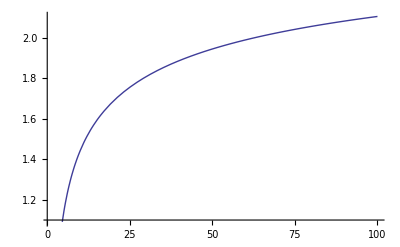

```mathematica
Plot[ EulerGamma-ExpIntegralEi[-Log[n]]-1/2 Log[-1/Log[n]]+1/2 Log[-Log[n]], {n,1,100}]
```

```mathematica
Limit[-ExpIntegralEi[-3 Log[n]]+ExpIntegralEi[-2 Log[n]]+1/2 Log[-3/(2 Log[n])]-1/2 Log[-1/(3 Log[n])]-1/2 Log[-2 Log[n]]+1/2 Log[-Log[n]],n->Infinity]
```

Log[3/2]

```mathematica
N[Log[Zeta[3]]]
```

0.184034

```mathematica
N[Log[3/2]]
```

0.405465

```mathematica
N[-Gamma[0,-Log[100]]]
```

30.1261+3.14159 ⅈ

```mathematica
Expand[Limit[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->0]]
```

-EulerGamma+ExpIntegralEi[Log[n]]+1/2 Log[1/Log[n]]-1/2 Log[Log[n]]

```mathematica
Expand[Limit[Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->0]]/.n->100
```

-EulerGamma-ⅈ π-Log[Log[100]]

```mathematica
Expand[Limit[-Gamma[0,(-1+s) Log[n]],s->0]]/.n->100
```

ⅈ π+ExpIntegralEi[Log[100]]

```mathematica
-EulerGamma-Log[-Log[n]]+ExpIntegralEi[Log[n]]+1/2 Log[1/Log[n]]+Log[-Log[n]]-1/2 Log[Log[n]]/.n->100
```

-EulerGamma+ExpIntegralEi[Log[100]]-Log[Log[100]]

```mathematica
tt[n_, s_,x_] := Sum[ (x^(k(1-s))-1)/k,{k,1,Log[x,n]}]
```

```mathematica
N[tt[100,3-I,1.000001]]
```

-2.90912+0.463656 ⅈ

```mathematica
N[LogIntegral[100]-Log[Log[100]]-EulerGamma]
```

28.0217

```mathematica
N[Expand[Limit[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s->-1]]/.n->100]
```

1215.32

```mathematica
N[ExpIntegralEi[(-2+I)Log[100]]-Log[(-2+I) Log[100]]-EulerGamma]
```

-2.90912+0.463656 ⅈ

```mathematica
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
```

```mathematica
N[D[zeta[100,s,-1,1],s]/.{s->0}]
```

-10.0174

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Lm1[n_,k_]:=Sum[Lm1[n/j,k-1],{j,2,n}]
Lm1[n_,1]:=Sum[Log[j],{j,2,n}]
Lm1[n_,0]:=UnitStep[n-1]
Lz[n_,z_]:=Sum[bin[z,k] Lm1[n,k],{k,1,Log[2,n]}]
Zm1[n_,k_,s_]:=Sum[j^-s Zm1[n/j,k-1,s],{j,2,n}]
Zm1[n_,0,s_]:=UnitStep[n-1]
Lz2[n_,z_]:=-Sum[bin[z,k] (D[Zm1[n,k,s],s]/.s->0)/k,{k,1,Log[2,n]}]
Lz3[n_,z_]:=D[-Sum[bin[z,k]/k  Zm1[n,k,s],{k,1,Log[2,n]}],s]/.s->0
```

```mathematica
N[Lm1[100,5]]
```

44.4803

```mathematica
-(N[D[Zm1[100,5,s],s]]/.s->0)/5
```

44.4803

```mathematica
N[Lz2[100,-1]]
```

-94.0453

```mathematica
N[Lz[100,-1]]
```

-94.0453

```mathematica
N[Lz3[100,-1]]
```

-94.0453

```mathematica
Limit[D[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s],s->0]
```

1-n+Log[n]

```mathematica
L2[n_,1,b_]:=L2[n,1,b]=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
L2[n_,k_,b_]:=Sum[L2[n/j,k-1,b],{j,2,n}]-b Sum[L2[n/(j b),k-1,b],{j,1,n}]
L1[n_,z_,c_]:=Sum[Binomial[z,k] L2[n,k,c],{k,0,Floor[Log[n]/Log[c]]}]
```

```mathematica
D1xD[n_,k_,x_]:=D1xD[n,k,x]=Sum[D1xD[n/(j+1),k-1,x]-x D1xD[n/(x j),k-1,x],{j,1,n}]
D1xD[n_,0,x_]:=UnitStep[n-1]
DxD[n_,z_,x_]:=Sum[Binomial[z,k] D1xD[n,k,x],{k,0,Log[x,n]}]
```

```mathematica
N[L2[100,1,2]]
```

-2.53088

```mathematica
D1xD[100,1,2]
```

-1

```mathematica
Limit[D[Gamma[0,s Log[n]],s],s->0]
```

-∞

```mathematica
Limit[D[-Log[(-1+s) Log[n]],s],s->0]
```

1

```mathematica
Limit[D[Log[s Log[n]],s],s->0]
```

∞

```mathematica
Limit[D[-Gamma[0,(-1+s) Log[n]]+Gamma[0,s Log[n]]-Log[(-1+s) Log[n]]+Log[s Log[n]],s],s->0]
```

1-n+Log[n]

```mathematica
Limit[D[Gamma[0,s Log[n]]+Log[s Log[n]],s],s->0]
```

Log[n]

```mathematica
Limit[D[-Gamma[0,(-1+s) Log[n]],s],s->0]
```

-n

```mathematica
D[-Gamma[0,(-1+s) Log[n]],s]
```

n^(1-s)/(-1+s)

```mathematica
D[-Log[(-1+s) Log[n]],s]
```

-1/(-1+s)

```mathematica
D[Gamma[0,s Log[n]],s]
```

-n^-s/s

```mathematica
D[Log[s Log[n]],s]
```

1/s

```mathematica
Expand[N[D[zeta[100,s,z,1]/z,s]/.{s->0}]]
```

-94.0453-169.15 z-81.6195 z^2-17.6846 z^3-1.19616 z^4-0.0438125 z^5

```mathematica
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Zm1[n_,s_,k_]:=Sum[j^-s Zm1[n/j,s,k-1],{j,2,n}]
Zm1[n_,s_,0_]:=UnitStep[n-1]
gg[n_, z_] :=Sum[ Expand[N[D[bin[z,k]Zm1[n,s,k]/z,s]]]/.s->0,{k,0,Log[2,n]}]
gga[n_, z_] :=Sum[ Expand[N[D[bin[z,k]Zm1[n,s,k],s]]]/.s->0,{k,0,Log[2,n]}]
ggar[n_, z_] :=-Sum[ Expand[N[D[(-1)^k /k Zm1[n,s,k],s]]]/.s->0,{k,1,Log[2,n]}]
ggk[n_, z_,k_] :=D[bin[z,k]Zm1[n,s,k]/z,s]/.s->0
ggk2[n_, k_] := Expand[N[D[Zm1[n,s,k],s]]]/.s->0
zeros[n_]:=List@@NRoots[gga[n,z]-1==0,z][[All,2]]
prod[n_,z_]:=1-Product[1-z/r,{r,zeros[n]}]
sum[n_]:=Sum[-1/r,{r,zeros[n]}]
zeros2[n_]:=List@@NRoots[gg[n,z]==0,z][[All,2]]
prod2[n_,z_]:=Product[1-z/r,{r,zeros2[n]}]
pggad[n_] :=Limit[D[Sum[ Expand[N[bin[z,k]Zm1[n,s,k]]]/.s->0,{k,0,Log[2,n]}],z],z->0]
ggad[n_] :=Limit[D[Sum[ Expand[N[D[bin[z,k]Zm1[n,s,k],s]]]/.s->0,{k,0,Log[2,n]}],z],z->0]
Lm1[n_,k_]:=(k/(k-1))Sum[Lm1[n/j,k-1],{j,2,n}]
Lm1[n_,1]:=Sum[-Log[j],{j,2,n}]
Lm1[n_,0]:=UnitStep[n-1]
zeros3[n_]:=List@@NRoots[N[Expand[D[zeta[n,s,z,1],s]/.s->0]]-1==0,z][[All,2]]
zeros3a[n_]:=List@@NRoots[N[Expand[zeta[n,s,z,1]/.s->0]]==0,z][[All,2]]

ggar[100,z]
```

-94.0453

```mathematica
gga[100,z]
```

0.-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
Expand[zeta[100,0,z,1]]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
N[Expand[D[zeta[100,s,z,1],s]/.s->0]]
```

-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
sum[100]
```

94.0453+0. ⅈ

```mathematica
prod[100,1]
```

-363.739+7.10543×10^-15 ⅈ

```mathematica
gga[100,1]
```

-363.739

```mathematica
zeros[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
zeros3[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
Sum[ -1/j,{j,zeros3[100]}]
```

94.0453+0. ⅈ

```mathematica
zeta[ 100, -0.010843552541250006, 0, 1]-1
```

0.

```mathematica
D[gga[100,z],z]/.z->0
```

-94.0453

```mathematica
zeros3[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
zeros3a[100]
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
5/4 4/3 3/2 2/1
```

5

```mathematica
N[Lm1[100,4]]
```

-779.857

```mathematica
ggk2[100,4]
```

-779.857

```mathematica
zeta[10,s,2,1]
```

1+2 (6^-s+7^-s+8^-s+9^-s+10^-s+4^-s (1+2^(-1-s))+5^-s (1+2^(-1-s))+3^-s (1+1/2 (2^-s+3^-s))+2^-s (1+1/2 (2^-s+3^-s+4^-s+5^-s)))

```mathematica
Integrate[t^(k-1)E^-t,{t,0,x}]bin[z,k] 1/(s-1)^k ((k-1)!)^-1/.k->3
```

((1-z) (2-z) z (2-Gamma[3,x]))/(12 (-1+s)^3)

```mathematica
Sum[Integrate[t^(k-1)E^-t bin[z,k] 1/(s-1)^k ((k-1)!)^-1,{t,0,x}],{k,0,Infinity}]
```

∑_(k=0)^∞ ConditionalExpression[-((-1)^k (-1+s)^-k z (Gamma[k]-Gamma[k,x]) Pochhammer[1-z,-1+k])/((-1+k)! k!),Re[k]>0]

```mathematica
Sum[t^(k-1)E^-t bin[z,k] 1/(s-1)^k ((k-1)!)^-1,{k,0,Infinity}]
```

(ⅇ^-t z Hypergeometric1F1[1-z,2,-t/(-1+s)])/(-1+s)

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
zeta1mxm1[n_,s_,k_, x_]:= Sum[ j^(-s)zeta1mxm1[n/j,s,k-1,x],{j,2,n}]-x Sum[ (j x)^(-s)zeta1mxm1[n/(x j),s,k-1,x],{j,1,n/x}]
zeta1mxm1[n_,s_,0,x_]:=UnitStep[n-1]
zeta1mx[n_,s_,z_,x_]:=Sum[ bin[z,k]zeta1mxm1[n,s,k,x],{k,0,If[x<2,Log[x,n],Log[2,n]]}]
logzeta1mx[n_,s_,x_]:=D[zeta1mx[n,s,z,x],z]/.z->0
L2[n_,1,x_]:=-(Sum[Log[j],{j,2,n}]-x Sum[Log[j x],{j,1,n/x}])
L2[n_,k_,x_]:=(k/(k-1))(Sum[L2[n/j,k-1,x],{j,2,n}]-x Sum[L2[n/(j x),k-1,x],{j,1,n}])
```

```mathematica
Expand[zeta1mx[100,0,z,101]]
logzeta1mx[100,0,2]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

4/5

```mathematica
N[D[zeta1mxm1[100,s,3,2],s]/.s->0]
```

17.9431

```mathematica
N[L2[100,3,2]]
```

17.9431

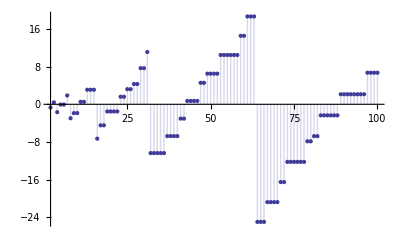

```mathematica
DiscretePlot[-N[D[logzeta1mx[n,s,2],s]/.s->0],{n,2,100}]
```

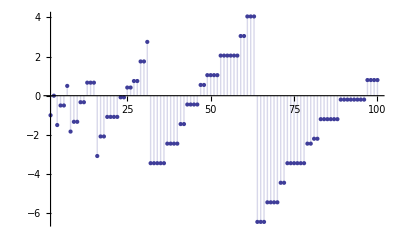

```mathematica
DiscretePlot[logzeta1mx[n,0,2],{n,2,100}]
```

```mathematica
D[(x^(k(1-s))-1)/k,s]/.s->0
```

-x^k Log[x]

```mathematica
Limit[ Sum[ -x^k Log[x],{k,1,Log[x,n]}],x->1]
```

1-n

```mathematica
D[ LogIntegral[n^(1-s)]-Log[Log[n^(1-s)]]-EulerGamma,s]/.s->0
```

1-n

```mathematica
Table[ (-1)^(j)Limit[bin[-z,j]/z,z->0],{j,1,10}]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10}

```mathematica
(-1)^(j)Limit[bin[z,j]/z,z->0]
```

-((-1)^(2 j) Gamma[j])/(j!)

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
zeta1mxm1[n_,s_,k_, x_]:= Sum[ j^(-s)zeta1mxm1[n/j,s,k-1,x],{j,2,n}]-x Sum[ (j x)^(-s)zeta1mxm1[n/(x j),s,k-1,x],{j,1,n/x}]
zeta1mxm1[n_,s_,0,x_]:=UnitStep[n-1]
zeta1mx[n_,s_,z_,x_]:=Sum[ bin[z,k]zeta1mxm1[n,s,k,x],{k,0,If[x<2,Log[x,n],Log[2,n]]}]
logzeta1mx[n_,s_,x_]:=D[zeta1mx[n,s,z,x],z]/.z->0
```

```mathematica
Table[FullSimplify[{n,7 z Expand[zeta1mx[Floor[n/7],0,z,aa=101]-zeta1mx[Floor[(n-1)/7],0,z,aa]],(Expand[zeta1mx[n,0,z,aa=101]-zeta1mx[n-1,0,z,aa]])-(Expand[zeta1mx[n,0,z,bb=7]-zeta1mx[n-1,0,z,bb]])}],{n,41,80}]//TableForm
```

41 | 0 | 0
42 | 7 z^3 | 7 z^3
43 | 0 | 0
44 | 0 | 0
45 | 0 | 0
46 | 0 | 0
47 | 0 | 0
48 | 0 | 0
49 | 7 z^2 | -7/2 z (-7+5 z)
50 | 0 | 0
51 | 0 | 0
52 | 0 | 0
53 | 0 | 0
54 | 0 | 0
55 | 0 | 0
56 | 7/6 z^2 (1+z) (2+z) | 7/6 z^2 (1+z) (2+z)
57 | 0 | 0
58 | 0 | 0
59 | 0 | 0
60 | 0 | 0
61 | 0 | 0
62 | 0 | 0
63 | 7/2 z^2 (1+z) | 7/2 z^2 (1+z)
64 | 0 | 0
65 | 0 | 0
66 | 0 | 0
67 | 0 | 0
68 | 0 | 0
69 | 0 | 0
70 | 7 z^3 | 7 z^3
71 | 0 | 0
72 | 0 | 0
73 | 0 | 0
74 | 0 | 0
75 | 0 | 0
76 | 0 | 0
77 | 7 z^2 | 7 z^2
78 | 0 | 0
79 | 0 | 0
80 | 0 | 0

```mathematica
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
Zm1[n_,0,s_]:=UnitStep[n-1]
Zm1[n_,k_,s_]:=Zm1[n,k,s]=Sum[j^-s Zm1[Floor[n/j],k-1,s],{j,2,n}]
zeta[n_, s_, z_] := Sum[ bin[ z,k] Zm1[ n,k,s],{k,0,Log[2,n]}]
zeros[n_,s_]:=List@@NRoots[zeta[n,s,z]==0,z][[All,2]]
zetaalt[n_,s_,z_]:=Product[1-z/r,{r,zeros[n,s]}]
```

```mathematica
zeros[100000,2]//TableForm
```

-96.3686-213.131 ⅈ
-96.3686+213.131 ⅈ
-31.144
-28.4883-44.9883 ⅈ
-28.4883+44.9883 ⅈ
-11.4956-16.6843 ⅈ
-11.4956+16.6843 ⅈ
-10.1417
-9.61048-4.61542 ⅈ
-9.61048+4.61542 ⅈ
-8.08137-9.15539 ⅈ
-8.08137+9.15539 ⅈ
-4.23774-12.2216 ⅈ
-4.23774+12.2216 ⅈ
3.95874-13.3611 ⅈ
3.95874+13.3611 ⅈ

```mathematica
zeros[1000000,2]//TableForm
```

-919.546
-98.5521
-56.5718-89.5194 ⅈ
-56.5718+89.5194 ⅈ
-19.7441-38.9516 ⅈ
-19.7441+38.9516 ⅈ
-12.2367-14.9262 ⅈ
-12.2367+14.9262 ⅈ
-11.7085
-11.2775-4.30913 ⅈ
-11.2775+4.30913 ⅈ
-9.95445-8.90915 ⅈ
-9.95445+8.90915 ⅈ
-7.84051-13.7037 ⅈ
-7.84051+13.7037 ⅈ
-2.63047-14.9893 ⅈ
-2.63047+14.9893 ⅈ
6.60545-15.3389 ⅈ
6.60545+15.3389 ⅈ

```mathematica
N[Expand[zeta[100000,2,z]]]
```

1.+0.497699 z+0.12385 z^2+0.0205441 z^3+0.00255436 z^4+0.000253471 z^5+0.0000207963 z^6+1.43262×10^-6 z^7+8.25343×10^-8 z^8+3.8963×10^-9 z^9+1.45011×10^-10 z^10+4.07809×10^-12 z^11+8.11705×10^-14 z^12+1.07464×10^-15 z^13+8.88423×10^-18 z^14+3.15853×10^-20 z^15+9.02612×10^-23 z^16

```mathematica
N[Log[Pi^2/6]^2]/2
```

0.123853